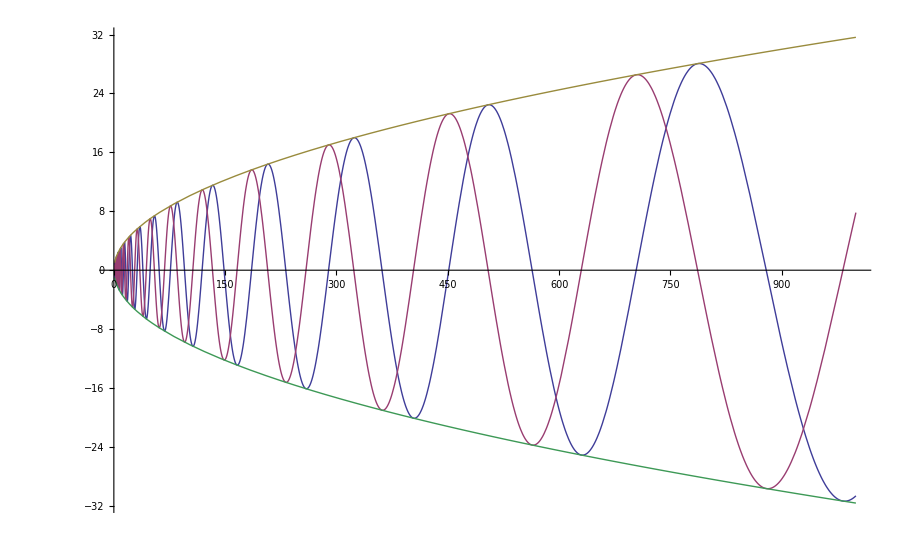

```mathematica
Plot[{Re[Gamma[ss=1,-(1-ZetaZero[1])Log[n]]],Im[Gamma[ss,-(1-ZetaZero[1])Log[n]]],Abs[Gamma[ss,-(1-ZetaZero[1])Log[n]]],-Abs[Gamma[ss,-(1-ZetaZero[1])Log[n]]]},{n,1,1000}]
```

```mathematica
Limit[ 1/c Sum[ 1, {j,1, c n}],{c->Infinity}]
```

{n}

```mathematica
Limit[ 1/c^2 Sum[ 1, {j,1, c^2 n},{k,1,c^2 n / j}],{c->Infinity}]
```

{Limit[n HarmonicNumber[c^2 n],c→∞]}

```mathematica
Limit[ 1/c^2 Sum[ 1, {j,1, c},{k,1,Floor[c^2 n / j]}],{c->Infinity}]
```

{Limit[(∑_(j=1)^c ∑_(k=1)^Floor[(c^2 n)/j] 1)/c^2,c→∞]}